Zadatak 1. Naći polinom p(x) koji interpolira funkciju f(x)=ⅇ^(-x^2) u tačkama x_0=0, x_1=1/2 i x_2=1. Oceniti grešku ove interpolacije u tačkama x∈[0,1].

```mathematica
xcv={0,1/2,1}
f[x_]=E^(-x^2);
cv=Table[{xcv[[i]],f[xcv[[i]]]},{i,1,Length[xcv]}]
```

{0,1/2,1}

{{0,1},{1/2,1/ⅇ^(1/4)},{1,1/ⅇ}}

```mathematica
pol[x_]=InterpolatingPolynomial[cv,x]//Expand//N
```

1.-0.252676 x-0.379444 x^2

```mathematica
treci[x_]=D[f[x],{x,3}]
```

12 ⅇ^(-x^2) x-8 ⅇ^(-x^2) x^3

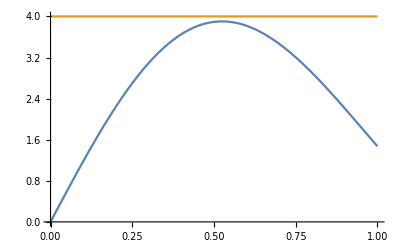

```mathematica
Plot[{Abs[treci[x]],4},{x,0,1}]
```

```mathematica
m3=4
```

4

```mathematica
greska[x_]=m3/(3!)Abs[Product[(x-cv[[i,1]]),{i,1,Length[cv]}]]
```

2/3 Abs[(-1+x) (-1/2+x) x]

```mathematica
greska[0.1]
```

0.024

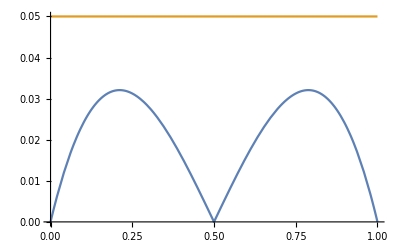

```mathematica
Plot[{greska[x],0.05},{x,0,1}]
```

```mathematica
greska[0.2]
```

0.032

Zadatak 2. Napisati program koji za dati skup čvorova, izračunava linearni interpolacioni splajn. Pretpostavićemo da su čvorovi sortirani (po prvoj koordinati).

```mathematica
zad2[cv_,x0_]:=Module[{},
m=Length[cv];
Do[
If[cv[[i,1]]<=x0<=cv[[i+1,1]],
rez=cv[[i,2]]+(cv[[i+1,2]]-cv[[i,2]])/(cv[[i+1,1]]-cv[[i,1]])(x0-cv[[i,1]])
],{i,1,m-1}
];
rez
]
```

```mathematica
cv={{0,1},{1,2},{3,1.7},{4,1.4},{5,0.5},{6,2},{7,0.2}};
```

```mathematica
zad2[cv,2.6]
```

1.76

Zadatak 3. Za dati skup čvorova {(0,1),(1,2),(3,4),(3.8,6.8),(5,5),(6,3.2),(8,0.9)} naći:
	a) polinom koji ih interpolira,
	b) linearni interpolacioni splajn,
	c) kubni interpolacioni splajn,
 a potom nacrtati sve tri funkcije i date čvorove zajedno na jednom grafiku.

```mathematica
cv={{0,1},{1,2},{3,4},{3.8,6.8},{5,5},{6,3.2},{8,0.9}}
```

{{0,1},{1,2},{3,4},{3.8,6.8},{5,5},{6,3.2},{8,0.9}}

```mathematica
pol[x_]=InterpolatingPolynomial[cv,x]//Expand
```

1.+16.0741 x-27.3823 x^2+15.882 x^3-4.01493 x^4+0.460761 x^5-0.0196871 x^6

```mathematica
sp1=Interpolation[cv,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
sp1[6.3]
```

2.855

```mathematica
sp3=Interpolation[cv,InterpolationOrder->3]
```

InterpolatingFunction[…]

```mathematica
sp3[6.3]
```

2.68877

```mathematica
gr1=ListPlot[cv];
gr2=Plot[{pol[x],sp1[x],sp3[x]},{x,0,8},PlotStyle->{Red,Green,Blue}];
```

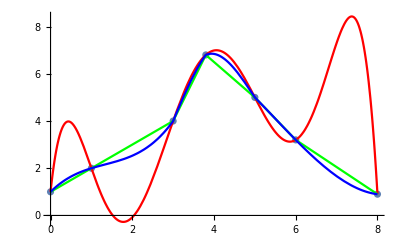

```mathematica
Show[gr1,gr2,PlotRange->All]
```